# Parsing Chemical Formulas and Equations

Anton Antonov

Mathematica

book for Wiley 2009-2010

## Introduction

Let us suppose that we want to write a program that balances chemical equations. If we, say, have the unbalanced equation

C_3 H_8+O_2-> C O_2+H_2 O,

that can be re-written as

a C_3 H_8+b O_2-> c C O_2+d H_2 O,

we want a program to find the stoichiometric coefficients a,b,c, and d.

Because of the law of conservation of masses, the amount of atoms of an element that appears on the left side of the equation should equal the amount of atoms that appear at right side of the equation. Therefore, the problem of balancing a chemical equation can be seen as a problem of solving a system of linear equations. A basic step of the Chemical Equation Balancer (CEB) is to find how many atoms of each element are on the left side and how many atoms of each element are on the right side. The mathematical background and programming of the CEB are described in the next chapter, "Chemical equation balancing."  In this chapter we are going to design and program an interpreter of strings representing chemical formulas. That interpreter, which we will call Chemical Formula Parser (CFP), would automatically recognize how many atoms of each element are in a chemical formula.

Let us explicitly formulate the problem we want to solve using the parser described in this chapter.

### Problem formulation

Given a string of the molecule formula of a chemical compound we want to compute various quantitative measures and statistics for the compound's molecule. More precisely, we want to find the total molecule mass, and the percentage of the mass that corresponds to each of the molecule's elements. For example, for the molecule C_6 H_12 O_6 we want to obtain the following data:

```mathematica
Block[{moleculeString="C6H12O6"},
Column[{
Row[{Style["Molecule formula: ",Bold,Italic],moleculeString}],
Row[{Style["Molecular mass: ",Bold,Italic],First[MolecularMassComposition[ParseMolecule[moleculeString]⟦1⟧]]}],"\n",Grid[Prepend[Transpose@Rest[MolecularMassComposition[ParseMolecule[moleculeString][[1]]]],Style[#,Bold,Italic]&/@{"Element ","Mass %","Atomic mass ","number of\natoms"}],Dividers->{None,{True,True,False}},Alignment->{{Left,Left,Left,Right}}]
}]
]
```

Molecule formula: C6H12O6
Molecular mass: 180.156


Element  | Mass % | Atomic mass  | number of
atoms
C | 0.40001 | 12.0107 | 6
H | 0.067138 | 1.00794 | 12
O | 0.53285 | 15.9994 | 6

In order to compute the quantitative measures we need to determine which elements and what number of their atoms are in the compound's molecule.

### Approaches

We are going to show two approaches to parsing molecules. The first one uses string matching patterns and it is described in the section "String match parser." Reading only that section would provide enough background to move to the next chapter,  "Chemical equation balancing." The second approach is to define in a formal manner the grammar of the chemical molecule notation, and using that grammar to program the concrete steps of the parser. The formal description of the chemical formulas notation would be done using the so called Backus-Naur Form (BNF), a language for grammar specification.

The reason we accentuate the second approach is that in general in engineering disciplines we prefer the use of standard solutions instead of particular (or peculiar) ones. By standard solutions here we mean solutions derived within a well understood theoretical or practical framework of concepts, approaches, and methodologies. Using these approaches and methodologies would, to a degree, guarantee the derivation of the required solution.

The method we follow in this chapter belongs to the theory of compilers, programs that translate code of human readable (or high order) programming languages to machine code which is readily executable. The method has the following steps:

Given a language describe its grammar in a formal manner using BNF or similar formalism.

For each rule of syntactical construction (or language pattern) choose a data structure that represents it.

Write a syntax analyzer (or parser) that from sequences of symbols produces syntactical structures defined by the grammar of the language.

For each rule of syntactical construction write an interpreting function based on the data structure that represents it.

Because we want the section "String matching parser" to be independent from the rest as much as possible, we are going to discuss first data constructs and interpretation.

### The rest of the chapter

### Thinks to speak about

#### Definitions

Lexical analysis

Syntactic analysis

Parser = Lexical analyser + Syntactic analyzer

Peoduction = BNF rule

Semantic analysis and Code generation

Syntactic structure = Parse tree

Handle is needed for parsing it is morpheme for terminals and BNF <symbol>

We show bottom-up parser. We use something similar to the shift-reduce parser. Also our grammar is simple precedence grammar, because we can invert to formula strings using the tree structure if we don't use the underscore and parenthesis around single element abbreviation. (Proof is needed that the Wirth-Weber precedence relationship holds.)

Our parser is also a predictive parser, because we have only one function for each non-terminal rule in our grammar.

#### Finite automata

WFinite automata

#### Formula representation with data structures

One way to approach this task is to transform the string that is the chemical formula into a data structure that is suitable for calculating molecular mass and what percentage to that mass is made by which elements.

We can think that a string of a molecule formula is composed of concatenated strings of sub-molecules.

#### Chemical formulas grammar

<element> :: = "H" | "He" | "Li" | "Be" | "B" | "C" | "N" | "O" | "F" | "Ne" | "Na" | "Mg" | "Al" | "Si" | "P" | "S" | "Cl" | "K" | "Ar" | "Ca" | "Sc" | "Ti" | "V" | "Cr" | "Mn" | "Fe" | "Ni" | "Co" | "Cu" | "Zn" | "Ga" | "Ge" | "As" | "Se" | "Br" | "Kr" | "Rb" | "Sr" | "Y" | "Zr" | "Nb" | "Mo" | "Tc" | "Ru" | "Rh" | "Pd" | "Ag" | "Cd" | "In" | "Sn" | "Sb" | "I" | "Te" | "Xe" | "Cs" | "Ba" | "La" | "Ce" | "Pr" | "Nd" | "Pm" | "Sm" | "Eu" | "Gd" | "Tb" | "Dy" | "Ho" | "Er" | "Tm" | "Yb" | "Lu" | "Hf" | "Ta" | "W" | "Re" | "Os" | "Ir" | "Pt" | "Au" | "Hg" | "Tl" | "Pb" | "Bi" | "Po" | "At" | "Rn" | "Fr" | "Ra" | "Ac" | "Pa" | "Th" | "Np" | "U" | "Am" | "Pu" | "Cm" | "Bk" | "Cf" | "Es" | "Fm" | "Md" | "No" | "Rf" | "Lr" | "Db" | "Bh" | "Sg" | "Mt" | "Rg" | "Hs" | "Ds" | "Uub" | "Uut" | "Uuq" | "Uup" | "Uuh" | "Uus" | "Uuo"

<digit> ::= "0"|"1"|"2"|"3"|"4"|"5"|"6"|"7"|"8"|"9"

<number> ::= <digit>|<digit><number>

<molecule> ::= <element>|<replicated>|<connected>|"("<molecule>")"

<replicated> ::= <molecule><number> | <molecule>"_"<number> | Subscript[<molecule>, <number>]

<connected> ::= <molecule><molecule>

<mix> ::= <molecule> | <molecule> "+ hν" | <mix> "+" <molecule>

<equation> ::= <mix> "->" <mix> | <mix> "=" <mix> | <mix> "⇆" <mix>

#### Example: Random molecule creation

<molecule>
<connected>
<molecule><molecule>
<molecule><replicated>
<element><element><number>
CO2

#### Example: Random equation creation

<equation>
<mix> -> <mix>
<molecule> + <molecule> -> <molecule> + <molecule>
<molecule><replicated> + <molecule><replicated> -> <molecule><replicated> + <replicated><molecule>
<element><element><number> + <element><element><number> -> <element><element><number> + <element><number><element>
CO2 + ClH4 -> CH3 + Cl3O

#### Parsing formulas into data structures

#### Parsing with StringMatchQ

```mathematica
moleculeString="C6H12O6";
```

```mathematica
StringCases["Ca3H4C12Mn",(cn:(CharacterRange["A","Z"]~~(CharacterRange["a","x"]|"")))~~(na:(NumberString|"")):>Molecule[cn,If[na=="",1,ToExpression[na]]]]
```

{Molecule[Ca,3],Molecule[H,4],Molecule[C,12],Molecule[Mn,1]}

```mathematica
StringCases["Ca3H4C12Mn",(cn:(CharacterRange["A","Z"]~~(CharacterRange["a","x"]|"")))~~(na:(NumberString|"")):>Molecule[cn,If[na=="",1,ToExpression[na]]]]//Timing
```

{0.000386,{Molecule[Ca,3],Molecule[H,4],Molecule[C,12],Molecule[Mn,1]}}

```mathematica
StringCases["(Ca3H4)2C12Mn",(cn:(CharacterRange["A","Z"]~~(CharacterRange["a","x"]|"")))~~(na:(NumberString|"")):>Molecule[cn,If[na=="",1,ToExpression[na]]]]//Timing
```

{0.000228,{Molecule[Ca,3],Molecule[H,4],Molecule[C,12],Molecule[Mn,1]}}

```mathematica
Union[StringTake[#,{1,1}]&/@elements]
%//Length
```

{A,B,C,D,E,F,G,H,I,K,L,M,N,O,P,R,S,T,U,V,W,X,Y,Z}

24

#### Other formulations

The first, most basic step is from given a molecule formula to find which elements and what number of their atoms compose that molecule formula.

These measures can be used for chemical equation balancing that we are going consider in the next chapter ("Chemical Equation Balancing"). In this chapter we are going to design and program an interpreter for strings of chemical formulas.

Chemical formulas can be interpreted as ideograms and sumarization of the chemical reactions they participate in, [Lazlo "Conventionalities in Formula Writing"], but we are going to see them as specifications of atoms presence in a molecule.

The chemical formulas can be seen as commands that have to interpreted in order to do symbolic manipulations that reflect the structure and properties of the compounds they represent. [Laz01]

### Code

```mathematica
Position[(ElementData[#,"Abbreviation"]&/@ElementData[]),"N"]
```

{{7}}

```mathematica
(ElementData["N","AtomicMass"]+ElementData["C","AtomicMass"])2+ElementData["Zn","AtomicMass"]
```

117.44

## Parsing and interpretation

The chemical formulas can be seen as words constructed using the grammatical rules of a certain language. Let us illustrate this using the notion of morpheme. Morpheme is defined as a single unit of meaning in a language. For example, the English word "unknowingly" has four morphemes: un, know, ing, and ly. Each of these morphemes contributes to the meaning of the word. Using the morpheme definition we can look at chemical formulas as words comprised of two types of morphemes: chemical element abbreviations, and numbers. For example, the chemical formula for propane, C_3 H_8, can be seen as a word that has four morphemes: C, 3, H, and 8.

Since we consider chemical formulas as words, we can extend that analogy and see chemical equations as sentences. The signs of summation and yielding can be seen as syntactical markers.

A typical compiler has the following phases:

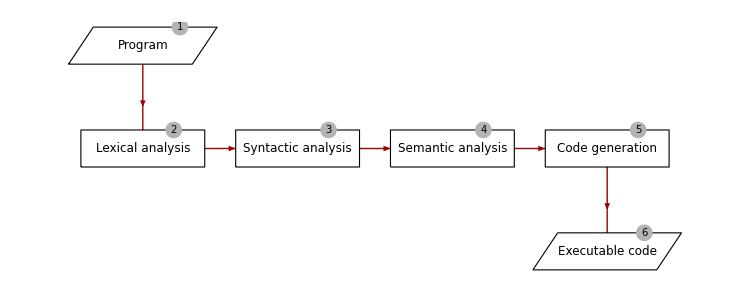

```mathematica
DefineCompilerVertex[{ffont_,fsize_,factor_}]:=
Block[{cl=0.8},
Clear[CompilerVertex,CompilerGraph];
CompilerVertex[coords_,"pinput"]:=IOElement[coords,{1,0.3}factor,Style["Program",fsize,FontFamily->ffont]];
CompilerVertex[coords_,"lexical"]:=
ProcessingElement[coords,{1,0.3}factor,Style["Lexical analysis",fsize,FontFamily->ffont]];
CompilerVertex[coords_,"syntactic"]:=
ProcessingElement[coords,{1,0.3}factor,Style["Syntactic analysis",fsize,FontFamily->ffont]];
CompilerVertex[coords_,"semantic"]:=
ProcessingElement[coords,{1,0.3}factor,Style["Semantic analysis",fsize,FontFamily->ffont]];
CompilerVertex[coords_,"codegeneration"]:=
ProcessingElement[coords,{1,0.3}factor,Style["Code generation",fsize,FontFamily->ffont]];
CompilerVertex[coords_,"poutput"]:=
IOElement[coords,{1,0.3}factor,Style["Executable code",fsize,FontFamily->ffont]];
CompilerGraph[]:={"pinput"->"lexical","lexical"->"syntactic","syntactic"->"semantic","semantic"->"codegeneration","codegeneration"->"poutput"}
];
DefineCompilerVertex[{"Times",12,1.5}]
DownDefineNumeratedVertex[DefineCompilerVertex,{"Times",12,1.2},{10,RGBColor[0.7,0.7,0.7]}]
DefineCompilerVertexNumerated[{"Times",12,1.2}]k=0;
LayeredGraphPlot[CompilerGraph[],VertexCoordinateRules->Join[{{1.5,1}},Table[{1.5i,0},{i,1,4}],{{6,-1}}],VertexRenderingFunction->(CompilerVertex[#1,#2]&),EdgeRenderingFunction->({RGBColor[0.6,0,0],Arrowheads[0.02], MidArrow[#1,#2,#3,"Ratio"->0.6,"LabelRatio"->0.47]}&),ImageSize->750]
```

Some or all of the phases can be combined. We do not need the code generation phase to solve our problem. We just want to interpret chemical formulas into molecular statistics. So we have the phases:

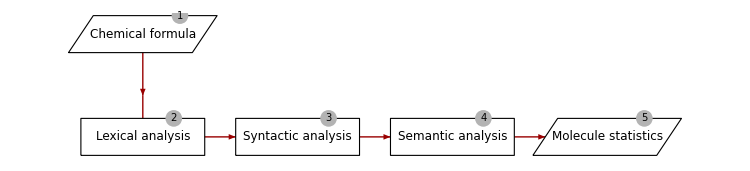

```mathematica
DefineCompilerVertex[{ffont_,fsize_,factor_}]:=
Block[{cl=0.8},
Clear[CompilerVertex,CompilerGraph];
CompilerVertex[coords_,"pinput"]:=IOElement[coords,{1,0.3}factor,Style["Chemical formula",fsize,FontFamily->ffont]];
CompilerVertex[coords_,"lexical"]:=
ProcessingElement[coords,{1,0.3}factor,Style["Lexical analysis",fsize,FontFamily->ffont]];
CompilerVertex[coords_,"syntactic"]:=
ProcessingElement[coords,{1,0.3}factor,Style["Syntactic analysis",fsize,FontFamily->ffont]];
CompilerVertex[coords_,"semantic"]:=
ProcessingElement[coords,{1,0.3}factor,Style["Semantic analysis",fsize,FontFamily->ffont]];
CompilerVertex[coords_,"codegeneration"]:=
ProcessingElement[coords,{1,0.3}factor,Style["Code generation",fsize,FontFamily->ffont]];
CompilerVertex[coords_,"poutput"]:=
IOElement[coords,{1,0.3}factor,Style["Molecule statistics",fsize,FontFamily->ffont]];
CompilerGraph[]:={"pinput"->"lexical","lexical"->"syntactic","syntactic"->"semantic","semantic"->"poutput"}
];
DefineCompilerVertex[{"Times",12,1.5}]
DownDefineNumeratedVertex[DefineCompilerVertex,{"Times",12,1.2},{10,RGBColor[0.7,0.7,0.7]}]
DefineCompilerVertexNumerated[{"Times",12,1.2}]k=0;
LayeredGraphPlot[CompilerGraph[],VertexCoordinateRules->Join[{{1.5,1}},Table[{1.5i,0},{i,1,4}]],VertexRenderingFunction->(CompilerVertex[#1,#2]&),EdgeRenderingFunction->({RGBColor[0.6,0,0],Arrowheads[0.02], MidArrow[#1,#2,#3,"Ratio"->0.6,"LabelRatio"->0.47]}&),ImageSize->750]
```

Applying this sequence of tasks to chemical formulas or equations, the lexical analyzer would recognize the morphemes and replace them with tokens that allow the syntax analyzer to easily identify them. The syntax analyser would produce data structure (a tree) that represents the syntactic structure of the formula or equation. (Most programing language syntactic analysers would typically use a tree data structure to represent the syntactic structure of a program.)

For example, Zn(CN)2 could be tokenized by the lexical analyzer to "[30] ([6][7])2" in which the atoms are replaced with integer identifiers placed in square brackets. From that last expression the syntax analyzer could produce a tree structure like

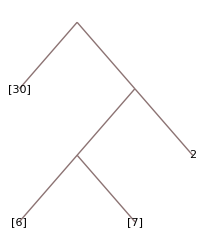

```mathematica
({"[30]",{{"[6]","[7]"},2}}//TreeForm)/.List->""
```

at each node n of which the semantic analyzer would generate (or execute) some code that depends on n. For example, using the tree above the semantic analyzer could replace all element identifiers with the corresponding atomic masses and use the operations of summation and multiplication at the relevant nodes in order to compute the molecular mass.

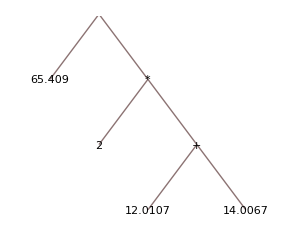

```mathematica
TreeForm[(Plus["[30]",Times[Plus["[6]","[7]"],2]])/.{Plus->"+",Times->"*","[30]"->ElementData["Zn","AtomicMass"],"[6]"->ElementData["C","AtomicMass"],"[7]"->ElementData["N","AtomicMass"]},PlotRange->{{-0.2,2.1},{0,2.6}}]
```

The molecular mass, 117.44, is the output of the semantic analyzer in this example.

The lexical analyzer can be seen as part of the syntactic analyzer. The CFP does not separate them. Also, CFP uses the abbreviated element names as element identificators.

## Backus-Naur Form

The notation system Backus-Naur Form (BNF) can be used to specify language grammars that are free of context.  (By "free of context" we mean that according to our BNF specification "O2H" is correct. The context of bonds, valency, etc. is not in the BNF specification.) The specification of a grammar using BNF is a list of rules. Each rule has a symbol on the left hand side, and one or more sequences of symbols on the right hand side. If there are more than one sequence on the right hand side they are separated with "|" that specifies alternative. Here is a rule

<product> ::= <term> | <term> <product>

This rule defines a product to be either a term or term written next to a product. Note that a symbol can appear both on the left and right hand sides. Symbols that do not appear on the left hand side are called terminals. Non-terminal symbols are start with the character '<' and end with the character '>' so they can be easily distinguished from the terminals. The symbol definition rules in BNF are called production rules, or productions.

Let us describe using BNF the admissible morphemes in chemical formulas. We can make the observation that the element names are abbreviated, the first letter is always a capital. Abbreviations are unique. We can enumerate all admissible elements as terminal symbols that comprise the rule for the symbol <element>.

<element> :: = "H" | "He" | "Li" | "Be" | "B" | "C" | "N" | "O" | "F" | "Ne" | "Na" | "Mg" | "Al" | "Si" | "P" | "S" | "Cl" | "K" | "Ar" | "Ca" | "Sc" | "Ti" | "V" | "Cr" | "Mn" | "Fe" | "Ni" | "Co" | "Cu" | "Zn" | "Ga" | "Ge" | "As" | "Se" | "Br" | "Kr" | "Rb" | "Sr" | "Y" | "Zr" | "Nb" | "Mo" | "Tc" | "Ru" | "Rh" | "Pd" | "Ag" | "Cd" | "In" | "Sn" | "Sb" | "I" | "Te" | "Xe" | "Cs" | "Ba" | "La" | "Ce" | "Pr" | "Nd" | "Pm" | "Sm" | "Eu" | "Gd" | "Tb" | "Dy" | "Ho" | "Er" | "Tm" | "Yb" | "Lu" | "Hf" | "Ta" | "W" | "Re" | "Os" | "Ir" | "Pt" | "Au" | "Hg" | "Tl" | "Pb" | "Bi" | "Po" | "At" | "Rn" | "Fr" | "Ra" | "Ac" | "Pa" | "Th" | "Np" | "U" | "Am" | "Pu" | "Cm" | "Bk" | "Cf" | "Es" | "Fm" | "Md" | "No" | "Rf" | "Lr" | "Db" | "Bh" | "Sg" | "Mt" | "Rg" | "Hs" | "Ds" | "Uub" | "Uut" | "Uuq" | "Uup" | "Uuh" | "Uus" | "Uuo"

We need to define numbers. A number is comprised of digits written next to each other. So we define a rule for what a digit is and use it in the definition of number. We define the symbol <digit> as one of the arabic numerals (which are terminal symbols).

<digit> ::= "0"|"1"|"2"|"3"|"4"|"5"|"6"|"7"|"8"|"9"

Now we can define the number symbol <number> recursively: a number is a digit or a digit written next to a number.

<number> ::= <digit>|<digit><number>

Next we need to define molecules. A molecule can be an element. Alternatively, a molecule can be put in parentheses. Alternatively, a molecule can be an element and a number next to it. Last, a molecule can also be recursively defined as a molecule written next to another molecule.

<molecule> ::= <element>|<submolecule>|<replicated>|<connected>

The first alternative, <element>, is already defined. The second alternative is needed to describe formulas like (Ce(SO_4))_2, i.e. (SO_4) is valid molecule, and it is derived from SO_4.

The rule of the second alternative <submolecule> simply says that parenthesis can placed a string that adheres to the rule of <molecule>.

<submolecule> ::= "("<molecule>")"

The rule for <submolecule> can be included in the rule <molecule>:

<molecule> ::= <element>|"("<molecule>")"|<replicated>|<connected>

But using a separate rule would make the program design easier to explain.

We define <replicated> as a molecule next to a number or a molecule, underscore, and a number next to each other.

<replicated> ::= <molecule><number> | <molecule>"_"<number>

We define <connected> simply as two molecules next to each other.

<connected> ::= <molecule><molecule>

Note that instead of having separate symbol <connected> we could have inserted its definition into the definition of <molecule>:

<molecule> ::= <element>|"("<molecule>")"|<replicated>|<molecule><molecule>

Next we want to define structures for chemical equations. We need to define grammatic rules Left Hand Side (LHS) and the Right Hand Side (RHS) of an equation and how LHS, yield sign, and RHS form an equation.

The structure of LHS and RHS is identical, so we are going to describe them with one production rule, for the symbol <mixture>.

<mixture> ::= <molecule> | <molecule> "+" "hν" | <mix> "+" <molecule>

Since there are multiple possibilities what charter or sequence of characters is used to show transformation between LHS mixtures and RHS mixtures, we define

<yield> ::= "→" | "->" | "=" | "⇆"

Now defining a production rule for a chemical equation is easy.

<equation> ::= <mixture> <yield> <mixture>

### Other formulations

(By "free of context" we mean the grammar and syntax of a sentence like "The cat is flying climbingly." is correct, but the meaning might be absent.)

## Data structures representing molecules

Here we are going to present a data structure that would represent the information contained in a chemical formula in a way more amenable for molecular composition calculations.

If we look at a molecule like copper(II) sulfate, CuSO_4, we discern it into three groups of symbols because of the three atoms it. We can see that formula as a list of three separate entities

```mathematica
{"Cu","S","O_4"}
```

We can name this structure, or in other words change the head to be something that reflects for  what purposes the structure is going to be used. We can use the head Molecule:

```mathematica
Molecule["Cu","S","O_4"]
```

Next we need to decide how to represent in the data structure formula parts that specify multiple atoms of a given element. We can choose a sub-structure that is an ordered list of an element name and an integer:

```mathematica
Molecule["Cu","S",{"O",4}]
```

Again, we can choose a head that is less generic than List, that identifies the data. We can (naively) look at CuSO_4 as CuSOOOO, and use the head Replicated:

```mathematica
Molecule["Cu","S",Replicated["O",4]]
```

The first element in the Replicated sub-structures can be a molecule not just an element name. For cerium(IV) sulfate, (Ce(SO_4))_2, we will have the representation

```mathematica
Molecule["Ce",Replicated[Molecule["S",Replicated["O",4]],2]]
```

Now using this data structure let us try to write Mathematica functions that use it to for different types of results. Let us start with programming the computation of molecular mass. We define the function MolecularMass for each type of sub-expressions we have in our structure.

```mathematica
MolecularMass[element_String]:=ElementData[element,"AtomicMass"];
MolecularMass[m_Molecule]:=Total[MolecularMass/@m];
MolecularMass[m_Replicated]:=MolecularMass[m⟦1⟧]*m⟦2⟧;
```

```mathematica
MolecularMass[Molecule["Cu","S",Replicated["O",4]]]
```

159.61

It would be nice if we can verify this result. If we change the definition that finds the atomic mass corresponding to an element abbreviation to return the element abbreviation itself i.e.

```mathematica
MolecularMass[element_String]:=element;
```

we can see that our implementation works correctly

```mathematica
MolecularMass[Molecule["Cu","S",Replicated["O",4]]]
```

Cu+4 O+S

because in to calculate the molecular mass from the expressions like the one above we simply replace element names with atomic masses.

Now let us program the conversion of a molecule data structure to a chemical formula (which is a string). As with MolecularMass we define the function MoleculeToString for each type of sub-expressions we have in our structure.

```mathematica
MoleculeToString[element_String]:=element;
MoleculeToString[m_Molecule]:=StringJoin@@Map[MoleculeToString,m];
MoleculeToString[m_Replicated]:=If[StringQ[m⟦1⟧],m⟦1⟧,"("<>MoleculeToString[m⟦1⟧]<>")"]<>ToString[m⟦2⟧];
```

Let us check the implementation

```mathematica
MoleculeToString[Molecule["Cu","S",Replicated["O",4]]]
```

CuSO4

Let us do another check using the molecule of zinc cyanide:

```mathematica
MoleculeToString[Molecule["Zn",Replicated[Molecule["C","N"],2]]]
```

Zn(CN)2

Last, let us write a function that finds the number of atoms of each element in the compound. The easiest way to program this is to expand the sub-expressions with the head Replicated and convert molecule expressions into lists of element names only. In other words we want to change

```mathematica
Molecule["Zn",Replicated[Molecule["C","N"],4]]
```

into

```mathematica
Molecule["Zn", Molecule["C", "N","C","N"]]
```

or better yet

```mathematica
Molecule["Zn", "C", "N","C","N"]
```

Then we can simply count the number of occurrences of each element. Let us clarify using actual code. We are going to take the molecule structure that corresponds to acetone, (CH_3)_2 CO

```mathematica
Molecule[Replicated[Molecule["C",Replicated["H",3]],2],"C","O"]
```

and expand the Replicated sub-expressions using ReplaceRepeated:

```mathematica
Molecule[Replicated[Molecule["C",Replicated["H",3]],2],"C","O"]//.Replicated[x_,n_]:>Table[x,{n}]
```

Molecule[{Molecule[C,{H,H,H}],Molecule[C,{H,H,H}]},C,O]

Next, we replace Molecule with List and flatten the expression:

```mathematica
Flatten[%/.Molecule->List]
```

{C,H,H,H,C,H,H,H,C,O}

At this point the number of atoms for each element can be found using the function Tally:

```mathematica
Tally[%]
```

{{C,3},{H,6},{O,1}}

Let us define a function executes the steps shown above for given molecule argument:

```mathematica
Clear[MoleculeToAtoms]
MoleculeToAtoms[mArg_Molecule]:=
Block[{m=mArg},
m=m//.Replicated[x_,n_]:>Table[x,{n}];
m=Flatten[m/.Molecule->List];
Sort[Tally[m]]
];
```

A simple test:

```mathematica
m=MoleculeToAtoms[Molecule[Replicated[Molecule["C",Replicated["H",3]],2],"C","O"]]
```

{{C,3},{H,6},{O,1}}

Although easy to invent and program, this method is both slow and memory consuming. (See Exercise 5.)

We can make another implementation, which is more in the spirit of the implementations of MolecularMass and MoleculeToString. i.e. give definition of MoleculeToAtoms for each type of sub-expressionin our data structure.

```mathematica
Clear[MoleculeToAtoms]
MoleculeToAtoms[element_String]:={{element,1}};
MoleculeToAtoms[r_Replicated]:={#⟦1⟧,#⟦2⟧*r⟦2⟧}&/@MoleculeToAtoms[r⟦1⟧];
MoleculeToAtoms[m_Molecule]:=
Sort[{#⟦1,1⟧,Total[#⟦All,2⟧]}&/@GatherBy[Join@@Map[MoleculeToAtoms,m],First]]
```

```mathematica
MoleculeToAtoms[Molecule[Replicated[Molecule["C",Replicated["H",3]],2],"C","O"]]
```

{{C,3},{H,6},{O,1}}

We can say that it was easy to program these functionalities, and conclude that the data structure chosen is adequate. The recursive calls each of these functions can be derived from the grammar described in the section "Backus-Naur Form."

## Data structures representing equations

From the production rule for <mixture> we can use the structure Mixture[_Molecule...] to represent LHS and RHS of an equation. From the production rule for <equation> we can use the structure Equation[_Mixture,_Mixture] to represent chemical equations.

For example, consider the unbalanced equation NO2 → N2O4. It is represented with the proposed structures as:

```mathematica
Equation[
Mixture[Molecule["N",Replicated["O",2]]],
Mixture[Molecule[Replicated["N",2],Replicated["O",4]]]
]
```

We can easily do various operations on that structure. Let us apply MolecularMass (defined above) to it:

```mathematica
Equation[
Mixture[Molecule["N",Replicated["O",2]]],
Mixture[Molecule[Replicated["N",2],Replicated["O",4]]]
]/.{m_Molecule:>MolecularMass[m]}
```

Equation[Mixture[46.0055],Mixture[92.011]]

[[ May here we should have some rudimentary balancing example ]]

## Finite State Machines

The concept of finite state machine can be used to explain and understand the work of many concrete or theoretical devices encountered in real life and sciences. A typical example of a finite state machine is a vending machine.

A vending machine at its initial state waits for one of two types of events to happen: (1) money deposit, or (2) correct dial pad code entry. If an event of type (1) happens the vending machine waits for an event of type (2) to happen. Similarly, if an event of type (2) happens the vending machine waits for an event of type (1) to happen. After an event of each type has happened, the vending machine checks is the amount of money deposited is enough to purchase an item corresponding to the code dialed. If yes, the machine checks does it have an item in stock. If yes, the machine would dispense an item. If the amount of the money deposited is larger than the amount of money required the vending machine would return change.

As we can see from this description the vending machine passes through various stages of event awaiting. The reaction to an event would change the vending machine state. For example, after dispensing an item, more money will be in the vending machine bank, and the vending machine will have one less item corresponding to the code dialed -- that is a state different from the state before dispensing the item. The vending machine has also intermediate states, like counting the deposited money, and buttons pressed.

Finite state machines have states, rules {_State, _Input}→_State how to switch from state to state, and actions, which depending on the machine, are associated with the rules or the states.

Let us introduce a type of diagrams called finite state machine diagrams

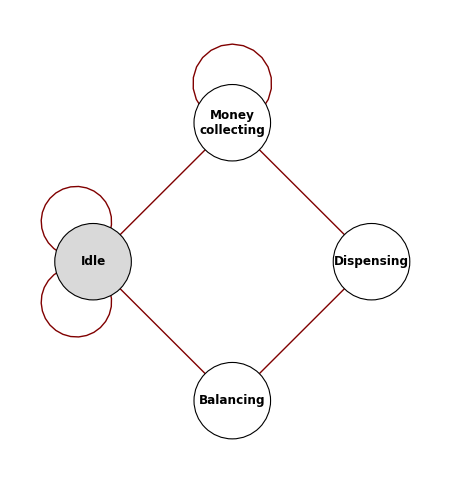

When parsing a chemical formula we

state digit accumulation

element accumulation

### Code

```mathematica
NewCoords[state_,coords_,value_]
```

```mathematica
Cockroach[stateChangingRules_][state_,coords_,value_]:=
Block[{newstate,newvalue,newcoords},
{newstate,newcoords,newvalue}={state,coords,value}/.stateChangingRules;

];
```

```mathematica
FL[cells_,s_]:=With[{nn=Length[Select[Flatten@cells,#>0&]]},Which[nn>4,0,cells⟦2,2⟧>0&&nn<3,0,nn==3&&cells⟦2,2⟧==0,2,cells⟦2,2⟧>1,1,True,cells⟦2,2⟧]];
ArrayPlot[#,ImageSize->40,Mesh->True]&/@CellularAutomaton[{FL,{},{1,1}},{{{0,1,0},{0,0,1},{1,1,1}},0},10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Clear[FL];
FL[cells_,s_]:=
Block[{},
If[cells⟦2,2⟧!=2,cells⟦2,2⟧,
(*ELSE*)
cells⟦2,2⟧=1;
]
];
ArrayPlot[#,ImageSize->40,Mesh->True]&/@CellularAutomaton[{FL,{},{1,1}},{{{0,1,0},{0,0,1},{1,1,1}},0},10]
```

## Parser of chemical formulas (first)

### The basic idea

[[ copied below ]]

### Extracting element name abbreviations

[[ copied below ]]

### Extracting numbers

This is straightforward. For example,

```mathematica
StringCases["12H10CrO5", RegularExpression["^\\d+"], 1]
```

{12}

### The parser as a finite state machine

```mathematica
stateTable=
{{"INIT","","WORD READ","tree=Molecule[]"},
{"WORD READ","formula⟦1⟧ is a letter","WORD READ","Accumulate letters to word, formula=Rest[formula]"},
{"WORD READ","formula⟦1⟧ is not a letter","ELEMENTS",""},
{"ELEMENTS","word is comprised of elements","POST-ELEMENTS","Append elements to tree"},
{"ELEMENTS","word has non-element sub-string","ERROREXIT","Message: wrong element(s)."},
{"POST-ELEMENTS","formula⟦1⟧ is a digit","NUMBER READ",""},
{"POST-ELEMENTS","formula⟦1⟧ is '_'","NUMBER READ","formula=Rest[formula]"},
{"POST-ELEMENTS","formula⟦1⟧ is '('","SUB-FORMULA-READ","formula=Rest[formula];level++"},
{"POST-ELEMENTS","formula⟦1⟧ is ')'","EXIT","formula=Rest[formula]; Return[{tree,formula}]"},
{"NUMBER READ","formula⟦1⟧ is a digit","NUMBER READ","Accumulate digits to num, formula=Rest[formula]"},
{"NUMBER READ","formula⟦1⟧ is not a digit","REPLICATION",""},
{"REPLICATION","Length[tree]==0","ERROREXIT","Message: number without an element."},
{"REPLICATION","Length[tree]>0","POST-REPLICATION","tree⟦-1⟧=Replicated[tree⟦-1⟧,num]"},
{"POST-REPLICATION","formula⟦1⟧ is a letter","WORD READ",""},
{"POST-REPLICATION","formula⟦1⟧ is '('","SUB-FORMULA-READ","formula=Rest[formula];level++"},
{"POST-REPLICATION","formula⟦1⟧ is '_'","ERROREXIT","Message: '_' is not allowed after a number"},
{"POST-REPLICATION","formula⟦1⟧ is ')'","EXIT","formula=Rest[formula]; Return[{tree,formula}]"},
{"SUB-FORMULA-READ","","INIT","oldtree=tree"},
{"EXIT","level==0","","Return[{tree,formula}]"},
{"EXIT","level>0","WORD READ","tree=Append[oldtree,tree];level--"}
};
Grid[Prepend[stateTable,Style[#,Bold,Italic]&/@{"state","input","new state","action"}],Dividers->All,Alignment->Left]
```

state | input | new state | action
INIT |  | WORD READ | tree=Molecule[]
WORD READ | formula⟦1⟧ is a letter | WORD READ | Accumulate letters to word, formula=Rest[formula]
WORD READ | formula⟦1⟧ is not a letter | ELEMENTS | 
ELEMENTS | word is comprised of elements | POST-ELEMENTS | Append elements to tree
ELEMENTS | word has non-element sub-string | ERROREXIT | Message: wrong element(s).
POST-ELEMENTS | formula⟦1⟧ is a digit | NUMBER READ | 
POST-ELEMENTS | formula⟦1⟧ is '_' | NUMBER READ | formula=Rest[formula]
POST-ELEMENTS | formula⟦1⟧ is '(' | SUB-FORMULA-READ | formula=Rest[formula];level++
POST-ELEMENTS | formula⟦1⟧ is ')' | EXIT | formula=Rest[formula]; Return[{tree,formula}]
NUMBER READ | formula⟦1⟧ is a digit | NUMBER READ | Accumulate digits to num, formula=Rest[formula]
NUMBER READ | formula⟦1⟧ is not a digit | REPLICATION | 
REPLICATION | Length[tree]==0 | ERROREXIT | Message: number without an element.
REPLICATION | Length[tree]>0 | POST-REPLICATION | tree⟦-1⟧=Replicated[tree⟦-1⟧,num]
POST-REPLICATION | formula⟦1⟧ is a letter | WORD READ | 
POST-REPLICATION | formula⟦1⟧ is '(' | SUB-FORMULA-READ | formula=Rest[formula];level++
POST-REPLICATION | formula⟦1⟧ is '_' | ERROREXIT | Message: '_' is not allowed after a number
POST-REPLICATION | formula⟦1⟧ is ')' | EXIT | formula=Rest[formula]; Return[{tree,formula}]
SUB-FORMULA-READ |  | INIT | oldtree=tree
EXIT | level==0 |  | Return[{tree,formula}]
EXIT | level>0 | WORD READ | tree=Append[oldtree,tree];level--

```mathematica
stateTable⟦All,1⟧//Union
%//Length
```

{ELEMENTS,EXIT,INIT,NUMBER READ,POST-ELEMENTS,POST-REPLICATION,REPLICATION,SUB-FORMULA-READ,WORD READ}

9

### The complete algorithm

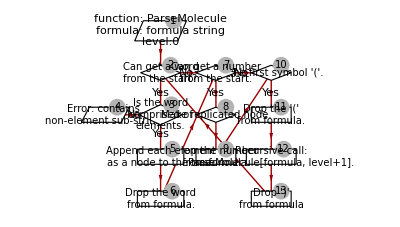

## Parser of chemical formulas

### The basic idea

We are going to program the parser in such a way that the lexical analysis is combined with the syntactical analysis. Why this is easier to do for the problem we are solving would become clear in the exposition below.

In order to program the parser let us all look at some examples of formulas and their syntactical structures. (I don't think programming can be done just considering abstract rules of a specification. One needs to think with concrete examples and contra-examples, and consider how they relate to the abstract specification. This point should be stated in the preface and/or in each chapter.)

Let us consider molecules like CaHIO3, CBrClF2, CHBrCl2. If we use instead of terminals their corresponding BNF symbols these formulas have the same syntactic structure -- see Figure 2.1.

Figure 2.1 Tree representation of the syntactic structure of CaHIO_3. The terminals "Ca", "H", "I", "O", and "3" are replaced with their BNF symbols, <element> and <number>.

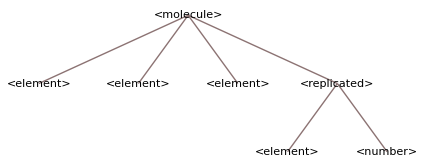

We can say that the syntactic structure is derived from the symbol <molecule> using the sequence of transformations shown in Table 2.1.

Table 2.1

```mathematica
Grid[Join[{Style[#,Bold,Italic]&/@{"","structure","rule applied"}},MapIndexed[Prepend[#,#2⟦1⟧]&,{{"<molecule>",""},{"<connected>","<molecule>"},{"<molecule><molecule>","<connected>"},{"<connected><connected>", "<molecule>"},{"<molecule><molecule><molecule><molecule>","<connected>"},{"<element><element><element><replicated>","<molecule>"},{"<element><element><element><element><number>","<replicated>"}}]],Alignment->{{Left,Center,Left},Automatic},Dividers->All,Frame->True]
```

| structure | rule applied
1 | <molecule> | 
2 | <connected> | <molecule>
3 | <molecule><molecule> | <connected>
4 | <connected><connected> | <molecule>
5 | <molecule><molecule><molecule><molecule> | <connected>
6 | <element><element><element><replicated> | <molecule>
7 | <element><element><element><element><number> | <replicated>

If we read the strings of these molecules from left to right, we are reading four element names and then we read a number. The number is applied to the last element name. Before reaching a digit we would read a number of letters -- these formulas can be split into two parts: an all letters one, and a digit one. The capital letters can seen as delimiters that separate the element names from each other. We also observe that if we append the element names to Molecule[], we will have almost correct syntactic structure, only the last node is incorrect. For example,

```mathematica
Fold[Append,Molecule[],{"Ca","H","I","O"}]
```

Molecule[Ca,H,I,O]

The last node needs to be converted to Replicated sub-expression with the number at the end of the formulas. We can do that using MapAt:

```mathematica
MapAt[Replicated[#,3]&,%,-1]
```

Molecule[Ca,H,I,Replicated[O,3]]

With these two operations we have obtained the correct syntactic structure.

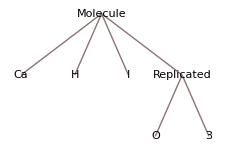

```mathematica
TreeForm[%]
```

If we think about all formulas that start with a capital letter, then using the above observations we can come up with the following algorithm:

1. The input is a string formula.

2. Initialize parse tree tree with Molecule[] .

3. Read letters until reaching a non-letter (a digit or a left parenthesis, according to the grammar). Split the formula into all letters part and all digits part.

4. Extract and validate element names from the all letters part. Append the element names to tree.

5. Make a number n from the all digits part and change the last node into Replicated[Last[tree],n].

This algorithm can be applied to the sub-strings between a matching pair of parenthesis. Therefore, we can call it recursively when we encounter "(" and make sure there is a closing ")".

Before giving the complete algorithm, let us resolve the questions of extracting and validating elements from the beginning of a chemical formula string.

### Extracting element name abbreviations

First let us get the element name abbreviations in suitably named variable:

```mathematica
elements=ElementData[#,"Abbreviation"]&/@ElementData[]
```

{H,He,Li,Be,B,C,N,O,F,Ne,Na,Mg,Al,Si,P,S,Cl,Ar,K,Ca,Sc,Ti,V,Cr,Mn,Fe,Co,Ni,Cu,Zn,Ga,Ge,As,Se,Br,Kr,Rb,Sr,Y,Zr,Nb,Mo,Tc,Ru,Rh,Pd,Ag,Cd,In,Sn,Sb,Te,I,Xe,Cs,Ba,La,Ce,Pr,Nd,Pm,Sm,Eu,Gd,Tb,Dy,Ho,Er,Tm,Yb,Lu,Hf,Ta,W,Re,Os,Ir,Pt,Au,Hg,Tl,Pb,Bi,Po,At,Rn,Fr,Ra,Ac,Th,Pa,U,Np,Pu,Am,Cm,Bk,Cf,Es,Fm,Md,No,Lr,Rf,Db,Sg,Bh,Hs,Mt,Ds,Rg,Uub,Uut,Uuq,Uup,Uuh,Uus,Uuo}

We are going to use the string pattern matching capabilities in Mathematica, and more precisely use regular expressions in StringCases. For example, using the regular expression string pattern "F[emr]?" we can extract from a string all element name abbreviations that start with "F".

```mathematica
StringCases["FrClBFmCHF2",RegularExpression["F[emr]?"]]
```

{Fr,Fm,F}

So let us divide the elements into groups of elements that start with the same letter. We can accomplish that by gathering them -- using GatherBy --  according to their first letter. (We also sort the result of GatherBy alphabetically.)

```mathematica
elementGroups=SortBy[Sort/@GatherBy[elements,StringTake[#,1]&],First];
elementGroups//ColumnForm
```

{Ac,Ag,Al,Am,Ar,As,At,Au}
{B,Ba,Be,Bh,Bi,Bk,Br}
{C,Ca,Cd,Ce,Cf,Cl,Cm,Co,Cr,Cs,Cu}
{Db,Ds,Dy}
{Er,Es,Eu}
{F,Fe,Fm,Fr}
{Ga,Gd,Ge}
{H,He,Hf,Hg,Ho,Hs}
{I,In,Ir}
{K,Kr}
{La,Li,Lr,Lu}
{Md,Mg,Mn,Mo,Mt}
{N,Na,Nb,Nd,Ne,Ni,No,Np}
{O,Os}
{P,Pa,Pb,Pd,Pm,Po,Pr,Pt,Pu}
{Ra,Rb,Re,Rf,Rg,Rh,Rn,Ru}
{S,Sb,Sc,Se,Sg,Si,Sm,Sn,Sr}
{Ta,Tb,Tc,Te,Th,Ti,Tl,Tm}
{U,Uub,Uuh,Uuo,Uup,Uuq,Uus,Uut}
{V}
{W}
{Xe}
{Y,Yb}
{Zn,Zr}

Then we construct a regular expression for each group.

```mathematica
elementGroupPatterns=
MapThread[
If[Length[#2]>0,
#1<>"["<>Apply[StringJoin,#2]<>"]"<>If[#3,"?",""],#1]&,
{StringTake[#⟦1⟧,{1}]&/@elementGroups,
Union[Flatten[Map[Characters[StringTake[#,{2,-1}]]&,#]]]&/@elementGroups,
MemberQ[#,StringTake[#⟦1⟧,{1}]]&/@elementGroups
},1]
```

{A[cglmrstu],B[aehikr]?,C[adeflmorsu]?,D[bsy],E[rsu],F[emr]?,G[ade],H[efgos]?,I[nr]?,K[r]?,L[airu],M[dgnot],N[abdeiop]?,O[s]?,P[abdmortu]?,R[abefghnu],S[bcegimnr]?,T[abcehilm],U[bhopqstu]?,V,W,X[e],Y[b]?,Z[nr]}

Then we combine the group regular expressions into one.

```mathematica
elementsPattern=StringJoin@@Riffle[elementGroupPatterns,"|"]
```

A[cglmrstu]|B[aehikr]?|C[adeflmorsu]?|D[bsy]|E[rsu]|F[emr]?|G[ade]|H[efgos]?|I[nr]?|K[r]?|L[airu]|M[dgnot]|N[abdeiop]?|O[s]?|P[abdmortu]?|R[abefghnu]|S[bcegimnr]?|T[abcehilm]|U[bhopqstu]?|V|W|X[e]|Y[b]?|Z[nr]

We can check and demonstrate that the pattern is working by applying it to random molecules from ChemicalData.

```mathematica
randomCompounds=ChemicalData[#,"CompoundFormulaString"]&/@ChemicalData["MetalCarbonyls"]⟦RandomInteger[{1,50},5]⟧
```

{C12H9O3W-3,C10H8CrO3,C7H7CrNO6,C10H8CrO3,C11H11MnO4}

```mathematica
randomCompoundElements=Map[StringCases[#,RegularExpression[elementsPattern]]&,randomCompounds]
```

{{C,H,O,W},{C,H,Cr,O},{C,H,Cr,N,O},{C,H,Cr,O},{C,H,Mn,O}}

```mathematica
Grid[Prepend[Transpose[{randomCompounds,randomCompoundElements}],Style[#,Bold,Italic]&/@{"formula","elements"}],Dividers->{All,Join[{True,True},Table[False,{Length[randomCompounds]-1}],{True}]},Alignment->Left]
```

formula | elements
C12H9O3W-3 | {C,H,O,W}
C10H8CrO3 | {C,H,Cr,O}
C7H7CrNO6 | {C,H,Cr,N,O}
C10H8CrO3 | {C,H,Cr,O}
C11H11MnO4 | {C,H,Mn,O}

Finaly, let us define a function that extracts the elements from the beginning of a string.

```mathematica
GetElements[formula_String]:=StringCases[formula,RegularExpression["A[cglmrstu]|B[aehikr]?|C[adeflmorsu]?|D[bsy]|E[rsu]|F[emr]?|G[ade]|H[efgos]?|I[nr]?|K[r]?|L[airu]|M[dgnot]|N[abdeiop]?|O[s]?|P[abdmortu]?|R[abefghnu]|S[bcegimnr]?|T[abcehilm]|U[bhopqstu]?|V|W|X[e]|Y[b]?|Z[nr]"]]
```

```mathematica
GetElements["C10H8CrO3"]
```

{C,H,Cr,O}

### Types of symbols

The algorithm of the parser would scan a chemical formula string from left to right. After a morpheme is found the data structure of the formula syntactic tree is updated, and the morpheme is deleted from the from the formula string.

Reading a formula from left to right we would encounter different combinations of characters. Using the BNF we can make the following observations.

There are five types of terminal symbols: capital letters, small letters, digits, left and right parenthesis, and the underscore.

All element names begin with a capital letter.

The underscore symbol is only followed by a digit.

The number of left parenthesis is the same as the number of right parenthesis.

Characters between a matching pair of parenthesis can be seen as separate chemical formulas. We will call these substrings sub-formulas.

Formulas and sub-formulas do not begin with a digit.

Not all sequences of characters appear. For example, a digit cannot be followed by the underscore. Let us find all possible occurrences allowed by the BNF of one type of characters followed by another.

Table 2.1 Character combinations and BNF transformation rules that produce them.

description | example | BNF symbol sequence | rule of derivation
a letter followed by a letter | ...ClF... | ...<element><element>... | <connected> → <element><element>
a letter followed by a digit | ...Cl2... | ...<element><number>... | <replicated> → <element><number>
a letter followed by _ | ...O_2... | ...<element>_<number>... | <replicated> → <element><number>
a letter followed by ( | ...H(Cl... | ...<element>"("<element>... | <connected> → <element><molecule>
a letter followed by (...( | ...H((Cl | ...<element>"("..."("<element>... | <connected> → <element><molecule>
a digit followed by a capital letter | ...2H... | ...<number><element>... | <replicated><element> or <replicated><replicated>
a digit followed by ( | ...2(Mn.. | ...<number>"("... | <replicated><molecule>
) followed by a capital letter | ...)C... | ...")"<element>... | <molecule><molecule>
) followed by a digit | ...)3... | ...")"<number>... | <replicated>
) followed by _ | ...)_3... | ...")"_<number>... | <replicated>
) followed by ( | ...)(C... | ...")""("<element>... | <molecule><molecule>
) followed by (...( | ...)((Cl... | ...")""("..."("<element>... | <connected> repeated

The table below shows what successions of characters are valid.

Table 2.2 Character type succession. A checkmark says that the character type of the corresponding row can be followed by the character of the corresponding column.

character type | capital
letter | small
letter | digit | ( | ) | _
capital letter | ✓ | ✓ | ✓ | ✓ | ✓ | ✓
small letter | ✓ | ✓ | ✓ | ✓ | ✓ | ✓
digit | ✓ |  | ✓ | ✓ | ✓ | 
( | ✓ |  |  | ✓ |  | 
) | ✓ |  | ✓ | ✓ | ✓ | ✓
_ |  |  | ✓ |  |  |

We can say that Table 2.1 suggests that the parser would have certain modes. Each group of that table corresponds to a different mode: element parsing mode, replication mode, and submolecule mode. The changes of the character types while reading the formula, would switch the parser from one mode to another. This process is illustrated with the graph on Figure 2.1. The gray oval node "Caller" does not represent a parsing mode but an initiation of the parsing. Each arrow shows transition from the arrow's source to arrow's target if a certain condition is met.

Figure 2.1 Parsing mode switching diagram. The chemical formula string is designated with the symbol "f." With f⟦1⟧ is designated the first symbol of f. The character ranges assume alphabetical order.

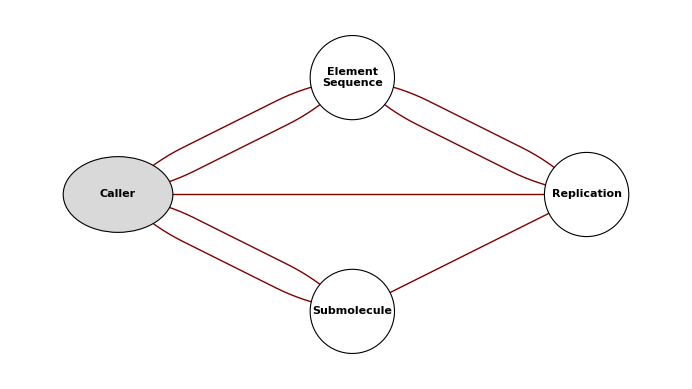

For each mode we can program a function that would take as arguments a formula string, syntactic tree, and the number of encountered left parentheses unmatched by right parentheses. According to its mode each function would drop characters from the begining of the formula string, change the syntactic tree, and either return the changed formula and tree as a result, or invoke another mode function using them as arguments.

### First implementation

#### Tests of the first character

Before proceeding further let us define for each type of characters a function that would give true if the first character in a formula belongs to function's type.

```mathematica
CapitalLetterFirstQ[s_String]:=StringMatchQ[s,StartOfString~~CharacterRange["A","Z"]~~___];
DigitFirstQ[s_String]:=StringMatchQ[s,StartOfString~~DigitCharacter~~___];
LeftParethesisFirstQ[s_String]:=StringMatchQ[s,StartOfString~~"("~~___];
RightParethesisFirstQ[s_String]:=StringMatchQ[s,StartOfString~~")"~~___];
UnderscoreFirstQ[s_String]:=StringMatchQ[s,StartOfString~~"_"~~___];
```

#### Element sequence parsing mode

Let us program the part of the parser that deals with the first group of character sequences in in Table 2.1. We note that in that first group except the "letter followed by letter" case in all the rest after the last letter read we encounter a non-letter character and hence we have already read a name of an element. If we reach a digit we need to switch into parsing a formula part described by <replicated>; if we reach left parenthesis we need to switch into parsing a sub-molecule. If the formula is empty or the first character is right parenthesis we return the data structure with the accumulated parsed entities.

```mathematica
ParseElementSequence[treeArg_Molecule,formulaArg_String,level_]:=
Block[{tree=treeArg,formula=formulaArg,w,t},
(* Extract elements from the begining of the formula string *)
w=StringCases[formula,RegularExpression["^[a-zA-Z]+"]];
w=w⟦1⟧;
t=GetElements[w];

(* Check for redundant letters *)
If[StringLength[StringJoin[t]]=!=StringLength[w],Return[$Failed]];

(* Drop the letters of the obtained elements *)
formula=StringDrop[formula,StringLength[w]];

(* Append each element name to the data structure *)
tree=Fold[Append,tree,t];

(* Choose an action according to the first character in the formula string *)
Which[
formula==""||(RightParethesisFirstQ[formula]&&level>0),{tree,formula,level},
DigitFirstQ[formula],ParseReplication[tree,formula,level],
UnderscoreFirstQ[formula],ParseReplication[tree,formula,level],
LeftParethesisFirstQ[formula],ParseSubMolecule[tree,formula,level],
True,$Failed
]

]/;CapitalLetterFirstQ[formulaArg];
```

#### Replication parsing mode

Next we are going to program the functions that react to reading a number. Or in other words, the functions that establish that the rule <connected> from BNF is applicable.

The production rule for the symbol <connected> gives two cases: (1) a <molecule> string and a <number> strin a separated by the underscore symbol, of (2) a <molecule> string and a <number> string a next to each other. We are going to give two definitions of the function ParseReplication, one for each case respectively.

Assume the first symbol of the string parsed in the underscore. Then according to BNF we expect a digit after it. We drop the underscore. If the first character is a digit then we have can say that we have reduced the first case to the second case, and hence, we call the second definition of the ParseReplication. If the fist character is not a digit, then we have an error. The first signature of ParseReplication corresponds to this algorithm:

```mathematica
ParseReplication[tree_Molecule,formulaArg_String,level_]:=
Block[{formula},

(* Drop the underscore symbol *)
formula=StringDrop[formulaArg,1];

(* Proceed with replication parsing if possible *)
If[DigitFirstQ[formula],
ParseReplication[tree,formula],
$Failed
]

]/;UnderscoreFirstQ[formulaArg];
```

Assume the first character of the parsed string is a digit. First we read all digits next to each other at the beginning of the parsed string. We drop them, and we make a number num from them (using FromDigits). Then, as explained in the sub-section "The basic idea" we change the last expression (node) in the parse tree from tree⟦-1⟧ to Replicated[tree⟦-1⟧,num]. Finaly, we test the first character of the (modified) parsed string, and call a corresponding function,  or return the (modified) parse tree as a result, or return failure. (See the parse mode switching diagram.) The second signature of ParseReplication corresponds to the algorithm outlined in this paragraph:

```mathematica
ParseReplication[treeArg_Molecule,formulaArg_String,level_]:=
Block[{tree=treeArg,formula=formulaArg,num},

(* Extract number from the begining of the formula string *)
num=StringCases[formula,RegularExpression["^\\d+"],1];
num=num[[1]];

(* Drop the characters of the number found *)
formula=StringDrop[formula,StringLength[num]];

(* Replicate the last parsed node *)
tree⟦-1⟧=Replicated[tree⟦-1⟧,FromDigits[num]];

(* Choose an action according to the first character in the formula *)
Which[
formula==""||RightParethesisFirstQ[formula]&&level>0,{tree,formula,level},
CapitalLetterFirstQ[formula],ParseElementSequence[tree,formula,level],
LeftParethesisFirstQ[formula],ParseSubMolecule[tree,formula,level],
True,$Failed
]

]/;DigitFirstQ[formulaArg];
```

#### Sub-molecule parsing mode

Next we are going to program the functions that react to reading a sub-molecule. Or in other words, the functions that establish that the rule <submolecule> from BNF is applicable.

Assume the first character of the parsed string is left parenthesis, '('. Then we drop and try to parse a molecule until we reach a matching right parenthesis, ')'. If failure does not occur, we append to the parse tree the parse tree of the sub-molecule. Finally, we test the first character of the (modified) parsed string, and call a corresponding function,  or return the (modified) parse tree as a result, or return failure. (See the parse mode switching diagram.)

```mathematica
Clear[ParseSubMolecule]
ParseSubMolecule[treeArg_Molecule,formulaArg_,level_]:=
Block[{tree=treeArg,formula,t,l},

(* Drop '(' from the begining of the formula *)
formula=StringDrop[formulaArg,1];

(* Recursive call in order to parse the submolecule *)
t=ParseMolecule[Molecule[],formula,level+1];
If[t===$Failed,Return[$Failed]];

(* Assign the submolecule tree and processed formula *)
{t,formula}=t;

(* If the parentheses are balanced, i.e. if there is a closing
')', append the submolecule structure to the tree and drop ')' *)
If[RightParethesisFirstQ[formula],
{tree,formula}={Append[tree,t],StringDrop[formula,1]},
Return[$Failed]
];

(* Choose an action according to the first character in the formula *)
Which[
formula=="",{tree,formula,level},
DigitFirstQ[formula],ParseReplication[tree,formula,level],
UnderscoreFirstQ[formula],ParseReplication[tree,formula,level],
LeftParethesisFirstQ[formula],ParseSubMolecule[tree,formula,level],
True,$Failed
]

]/;LeftParethesisFirstQ[formulaArg];
```

#### The caller

Given a formula, we have to decide should we start with parsing an element sequence (if the first character is capital letter) or we should start with parsing a sub-molecule (if the first character is left parenthesis) or give failure. (See "Caller" node on Figure 2.1.)

```mathematica
ParseMolecule[formula_String]:=
ParseMolecule[Molecule[],formula,0];
ParseMolecule[treeArg_,formulaArg_,levelArg_]:=
Block[{t,tree,formula,level},
{tree,formula,level}={treeArg,formulaArg,levelArg};
t=
Which[
CapitalLetterFirstQ[formula],ParseElementSequence[tree,formula,level],
LeftParethesisFirstQ[formula],ParseSubMolecule[tree,formula,level],
True,$Failed
];
If[t===$Failed,t,Most[t]]
];
```

### Parsing examples

```mathematica
ParseMolecule["Zn(SO2)3"]
```

{Molecule[Zn,Replicated[Molecule[S,Replicated[O,2]],3]],}

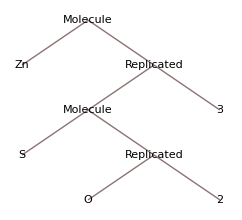

```mathematica
TreeForm[%⟦1⟧]
```

### Code

#### BNF symbol sequence cases

```mathematica
symbolSequenceCases=
{{{"a letter followed by a letter","...ClF...","...<element><element>...","<connected> → <element><element>"},{"a letter followed by a digit","...Cl2...","...<element><number>...","<replicated> → <element><number>"},{"a letter followed by _","...O_2...","...<element>_<number>...","<replicated> → <element><number>"},{"a letter followed by (","...H(Cl...","...<element>\"(\"<element>...","<connected> → <element><molecule>"},{"a letter followed by (...(","...H((Cl","...<element>\"(\"...\"(\"<element>...","<connected> → <element><molecule>"}},{{"a digit followed by a capital letter","...2H...","...<number><element>...","<replicated><element> or <replicated><replicated>"},{"a digit followed by (","...2(Mn..","...<number>\"(\"...","<replicated><molecule>"}},{{") followed by a capital letter","...)C...","...\")\"<element>...","<molecule><molecule>"},{") followed by a digit","...)3...","...\")\"<number>...","<replicated>"},{") followed by _","...)_3...","...\")\"_<number>...","<replicated>"},{") followed by (","...)(C...","...\")\"\"(\"<element>...","<molecule><molecule>"},{") followed by (...(","...)((Cl...","...\")\"\"(\"...\"(\"<element>...","<connected> repeated"}}};
symbolSequenceCases⟦All,All,1⟧=Map[Style[#,FontFamily->Times]&,symbolSequenceCases⟦All,All,1⟧,{2}];
Grid[Prepend[Join@@symbolSequenceCases,Style[#,Bold,Italic]&/@{"description","example","BNF symbol sequence","rule of derivation"}],Dividers->{All,Prepend[Flatten[Riffle[Map[Table[False,{#-1}]&,Length/@symbolSequenceCases],True,{1,-1,2}]],True]},Alignment->{{Left,Center,Left,Left},Center}]
```

description | example | BNF symbol sequence | rule of derivation
a letter followed by a letter | ...ClF... | ...<element><element>... | <connected> → <element><element>
a letter followed by a digit | ...Cl2... | ...<element><number>... | <replicated> → <element><number>
a letter followed by _ | ...O_2... | ...<element>_<number>... | <replicated> → <element><number>
a letter followed by ( | ...H(Cl... | ...<element>"("<element>... | <connected> → <element><molecule>
a letter followed by (...( | ...H((Cl | ...<element>"("..."("<element>... | <connected> → <element><molecule>
a digit followed by a capital letter | ...2H... | ...<number><element>... | <replicated><element> or <replicated><replicated>
a digit followed by ( | ...2(Mn.. | ...<number>"("... | <replicated><molecule>
) followed by a capital letter | ...)C... | ...")"<element>... | <molecule><molecule>
) followed by a digit | ...)3... | ...")"<number>... | <replicated>
) followed by _ | ...)_3... | ...")"_<number>... | <replicated>
) followed by ( | ...)(C... | ...")""("<element>... | <molecule><molecule>
) followed by (...( | ...)((Cl... | ...")""("..."("<element>... | <connected> repeated

#### Which symbols can follow a given symbol

```mathematica
characterType=Style[#,Bold,Italic]&/@{"capital letter","small letter","digit","(",")","_"};
canBeFollowed={
{True,True,True,True,True,True},
{True,True,True,True,True,True},
{True,False,True,True,True,False},
{True,False,False,True,False,False},
{True,False,True,True,True,True},
{False,False,True,False,False,False}};
Grid[
Join[
{Join[{Style["character type",Bold,Italic]},characterType/.s_String:>StringReplace[s," "->"\n"]]},
MapThread[Prepend[#2,#1]&,{Style[#,Bold]&/@characterType,canBeFollowed/.{True->"✓",False->""}}]
],
ItemSize->{Join[{8},Table[5,{Length[characterType]}]],Automatic},
Dividers->{Join[{True,True},Table[False,{5}],{True}],Join[{True,True},Table[True,{5}],{True}]},Alignment->Left]
```

character type | capital
letter | small
letter | digit | ( | ) | _
capital letter | ✓ | ✓ | ✓ | ✓ | ✓ | ✓
small letter | ✓ | ✓ | ✓ | ✓ | ✓ | ✓
digit | ✓ |  | ✓ | ✓ | ✓ | 
( | ✓ |  |  | ✓ |  | 
) | ✓ |  | ✓ | ✓ | ✓ | ✓
_ |  |  | ✓ |  |  |

#### Check first letter test functions

```mathematica
Outer[#1[#2]&,{CapitalLetterFirstQ,DigitFirstQ,LeftParethesisFirstQ,RightParethesisFirstQ,UnderscoreFirstQ},{"HC12","123Ca","(CH2)",")2C12","_45C12"}]//TableForm
```

True | False | False | False | False
False | True | False | False | False
False | False | True | False | False
False | False | False | True | False
False | False | False | False | True

## Parser of chemical equations

After we have implemented a parser for chemical formulas, parsing a chemical formula seems easy. Given a string with a chemical equation, we start parsing it to get a molecule. That molecule would belong to the left hand side of the equation. If we reach a plus sign we drop it and continue to parse another molecule. If we reach a yield sign we drop it and start parsing molecules for the right hand sign.

So to summarize, in order to parse a chemical equation we need to call the chemical formula parser in between signs for mixing, '+', and yield, '→', '->' , '='. This can be illustrated with the diagram on Figure 2.2.

Figure 2.2

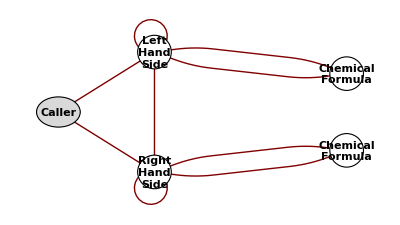

Let us describe the process outlined on Figure 2.2. The "Caller" has string containing a chemical equation. With that string start with a character that is valid first character according to the grammar for chemical formulas, the parser switches to the "Left Hand Side" parsing mode. In that mode if the parsed string starts with a capital letter or left parenthesis, the parser switches to a "Chemical Formula" parsing mode that switches back to "Left Hand Side" if it reaches '+' or a yield sign. If '+' is reached "Left Hand Side" would not switch to another mode (and drop '+' from the parsed string). If the one of the yield signs is reached "Left Hand Side" would switch to "Right Hand Side."  If the first character is the parsed string is a capital letter or a left parenthesis, "Right Hand Side" would switch to "Chemical Formula." When called by the "Right Hand Side," "Chemical Formula" would switch back without an error if the plus sign is encountered or the parsed string becomes empty. "Right Hand Side" switches to "Caller" if the parsed string becomes empty.

### Implementation using the state diagram

In this sub-section we are going implement the parser according to Figure 2.2. We can say that the (defined below) functions YieldSignFirstQ amd YieldSign2FirstQ implement the prdocution rule for <yield>, and the functions LeftHandSide and RightHandSide -- the former is calling the later -- are implementing production rule for <equation>.

#### Additional first symbol tests

First we need some additional definitions for the production rule for the BNF symbol <yield>. We going to separate the single character yield signs from the two character yield signs. That makes the removal of the yield signs from the parsed string more convenient. (See the definition of LeftHandSide.)

```mathematica
YieldSignFirstQ[s_String]:=StringMatchQ[s,RegularExpression["^[→|=|⇆].*"]];
YieldSign2FirstQ[s_String]:=StringMatchQ[s,RegularExpression["^\\-\\>.*"]];
```

#### The left hand side

The "Left Hand Side" parsing mode is invoked if the first character is a capital letter or a left parenthesis. "Left Hand Side" calls CFP and filters out the plus signs in between the chemical formulas. If a yield sign is encountered a switch to "Right Hand Side" is made. If CFP fails then "Left Hand Side" fails too. "Left Hand Side" also fails if parsed string has unexpected symbols of if its end is reached.

```mathematica
LeftHandSide[treeArg_,equationArg_String]:=
Block[{t,tree=treeArg},

t=ParseMolecule[equationArg];
If[t===$Failed,Return[$Failed]];

tree=MapAt[Append[#,t⟦1⟧]&,tree,1];
t=t⟦2⟧;

Which[
PlusFirstQ[t],LeftHandSide[tree,StringDrop[t,1]],
YieldSignFirstQ[t],RightHandSide[tree,StringDrop[t,1]],
YieldSign2FirstQ[t],RightHandSide[tree,StringDrop[t,2]],
True,$Failed
]

]/;(LeftParethesisFirstQ[equationArg]||CapitalLetterFirstQ[equationArg]);
```

#### The right hand side

The "Right Hand Side" is invoked from "Left Hand Side" after the later reaches a yield sign and after the yield sign the parsed string has a capital letter or a left parenthesis. As "Left Hand Side," "Right Hand Side" calls CFP and filters out the plus signs in between the chemical formulas. "Right Hand Side" fails if unexpected symbols are encountered in the parsed string.

```mathematica
RightHandSide[treeArg_,equationArg_String]:=
Block[{t,tree=treeArg},

t=ParseMolecule[equationArg];
If[t===$Failed,Return[$Failed]];

tree=MapAt[Append[#,t⟦1⟧]&,tree,2];
t=t⟦2⟧;

Which[
t==="",{tree,t},
PlusFirstQ[t],RightHandSide[tree,StringDrop[t,1]],
True,$Failed
]

]/;(LeftParethesisFirstQ[equationArg]||CapitalLetterFirstQ[equationArg]);
```

#### The caller

Given a chemical equation, we have to decide should we start with parsing its left hand side or give failure. (See "Caller" node on Figure 2.2.) We also initialize the parse tree structure to be and equation with empty LHS and RHS, i.e. Equation[Mix[],Mix[]].

```mathematica
ChemicalEquationParser[equationArg_String]:=
Module[{equation=StringReplace[equationArg," "->""],t,tree=Equation[Mix[],Mix[]],molecule},

If[LeftParethesisFirstQ[equationArg]||CapitalLetterFirstQ[equationArg],
t=LeftHandSide[tree,equation],
$Failed
]

];
```

### Implementation using a loop

```mathematica
Clear[ChemicalEquationParser];
ChemicalEquationParser[equationArg_String]:=
Module[{equation=equationArg,t,lhs={},rhs={},side="LHS",molecule},
While[StringLength[equation]>0&&t=!=$Failed,
t=ParseMolecule[equation];
If[t===$Failed,Return[$Failed]];

{molecule,equation}=t;
If[side=="LHS",AppendTo[lhs,molecule],AppendTo[rhs,molecule]];

If[StringLength[equation]>0,
t=StringCases[equation,StartOfString~~WhitespaceCharacter...~~"+"~~WhitespaceCharacter...];
(*Print[t];*)
If[t==={},
If[side=="LHS",t=StringCases[equation,StartOfString~~WhitespaceCharacter...~~("->"|"→"|"<->"|"↔"|"=")~~WhitespaceCharacter...];
If[t==={},Return[$Failed]];
side="RHS",
(*ELSE*)
Return[$Failed]
];
];
equation=StringTake[equation,{StringLength[t⟦1⟧]+1,-1}];
];
(*Print[equation];*)
];
{lhs,rhs,equation}
];
```

### Examples of parsing chemical equations

```mathematica
ChemicalEquationParser["NO2+C2->CNO2"]
```

{Equation[Mix[Molecule[N,Replicated[O,2]],Molecule[Replicated[C,2]]],Mix[Molecule[C,N,Replicated[O,2]]]],}

```mathematica
ChemicalEquationParser["NO2 + C2 -> CNO2"]
```

{Equation[Mix[Molecule[N,Replicated[O,2]],Molecule[Replicated[C,2]]],Mix[Molecule[C,N,Replicated[O,2]]]],}

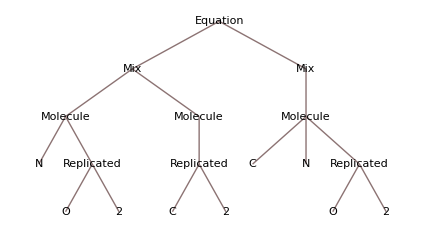

```mathematica
TreeForm[%⟦1⟧]
```

## String matching parser

### Definitions

```mathematica
specieSP=(CharacterRange["A","Z"]~~(CharacterRange["a","x"]|""))~~(NumberString|"");
```

```mathematica
Clear[StringsToMolecule]
StringsToMolecule[ename_,na_String]:=If[na=="",ename,Replicated[ename,ToExpression[na]]];
```

```mathematica
Clear[ParseMolecule,ParseSubMolecule]
ParseMolecule[moleculeArg_String]:=
Block[{t=ParseSubMolecule[moleculeArg]},If[Head[t]=!=Molecule,Molecule[t],t]];
ParseSubMolecule[moleculeArg_String]:=
Block[{braced,notbraced},PRINT["general"];
braced=StringCases[moleculeArg,("("~~(specieSP...)~~")"~~(NumberString|""))];
Molecule@@Map[ParseSubMolecule,StringSplit[moleculeArg,Thread[braced->braced]]]
];
ParseSubMolecule[moleculeArg_String]:=
Block[{t},PRINT["( & ) free"];
t=StringCases[moleculeArg,(en:(CharacterRange["A","Z"]~~(CharacterRange["a","x"]|"")))~~(na:(NumberString|"")):>StringsToMolecule[en,na]];
If[Length[t]==1,t⟦1⟧,Molecule@@t]
]/;StringFreeQ[moleculeArg,{"(",")"}];
ParseSubMolecule[moleculeArg_String]:=
Block[{t},PRINT["(~~___~~)"];
t=StringCases[moleculeArg,StartOfString~~"("~~x___~~")"~~(nm:(NumberString|""))~~EndOfString:>StringsToMolecule[ParseSubMolecule[x],nm]];
If[Length[t]==1,t⟦1⟧,Molecule@@t]
]/;StringMatchQ[moleculeArg,StartOfString~~"("~~___~~")"~~(NumberString|"")~~EndOfString];
```

```mathematica
ParseMolecule["(Ca3H4)2"]
```

Molecule[Replicated[Molecule[Replicated[Ca,3],Replicated[H,4]],2]]

```mathematica
ParseMolecule["(Ca3H4)2"]
ParseMolecule["(Ca3H4(Ca4O3)4)2"]
```

Molecule[Replicated[Molecule[Replicated[Ca,3],Replicated[H,4]],2]]

Molecule[Replicated[Molecule[Molecule[Replicated[Ca,3],Replicated[H,4]],Replicated[Molecule[Replicated[Ca,4],Replicated[O,3]],4]],2]]

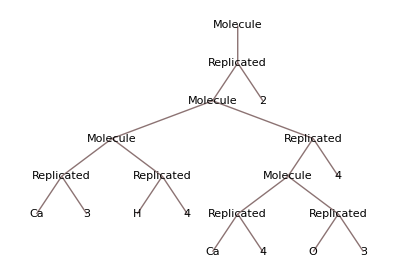

```mathematica
ParseMolecule["(Ca3H4(Ca4O3)4)2"]//TreeForm
```

```mathematica
ParseMolecule["(Ca3H4(Ca4O3)4)2"]//MolecularMass
```

2 (3 Ca+4 H+4 (4 Ca+3 O))

```mathematica
ParseMolecule["(Ca3H4(Ca4O3)4)2"]/.{Replicated->Times,Molecule->Plus}
%/.atomicWeightsRule
```

2 (3 Ca+4 H+4 (4 Ca+3 O))

1915.

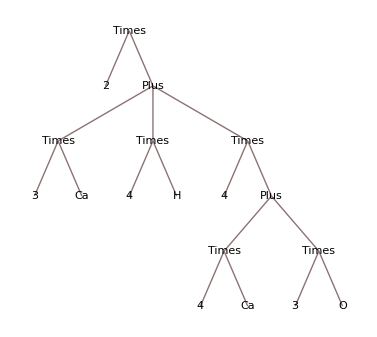

```mathematica
TreeForm[%]
```

```mathematica
ParseMolecule["Ca3H4(Ca4O3)4C12(H2Mn4)5"]
```

Molecule[Molecule[SelfJoined[Ca,3],SelfJoined[H,4]],SelfJoined[Molecule[SelfJoined[Ca,4],SelfJoined[O,3]],4],SelfJoined[C,12],SelfJoined[Molecule[SelfJoined[H,2],SelfJoined[Mn,4]],5]]

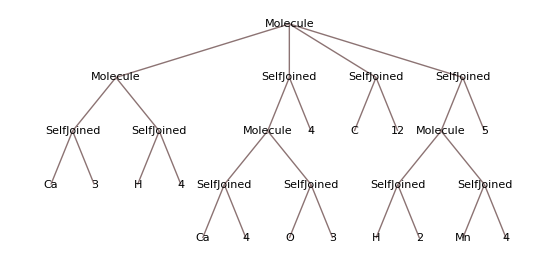

```mathematica
TreeForm[%]
```

```mathematica
PRINT=.
ParseSubMolecule["(Ca3H4)2C12(C2H5)Mn"]
```

Molecule[SelfJoined[Molecule[SelfJoined[Ca,3],SelfJoined[H,4]],2],SelfJoined[C,12],Molecule[SelfJoined[C,2],SelfJoined[H,5]],Mn]

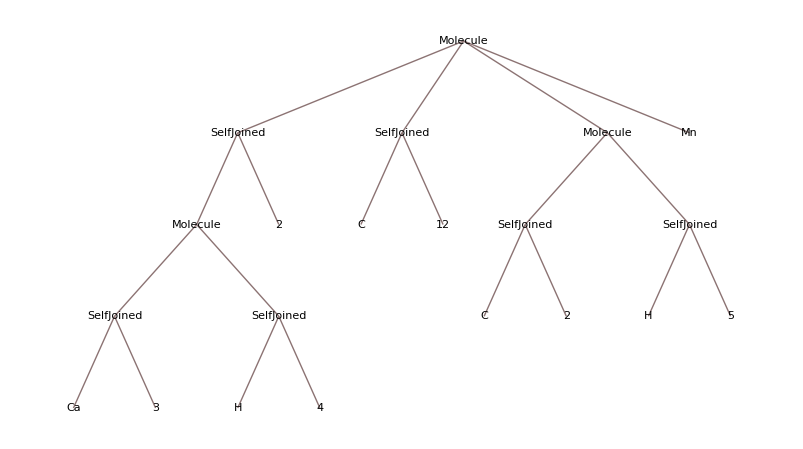

```mathematica
TreeForm[%]
```

Molecule[SelfJoined[Molecule[SelfJoined[Ca,3],SelfJoined[H,4]],2],SelfJoined[C,12],Molecule[SelfJoined[C,2],SelfJoined[H,5]],Mn]

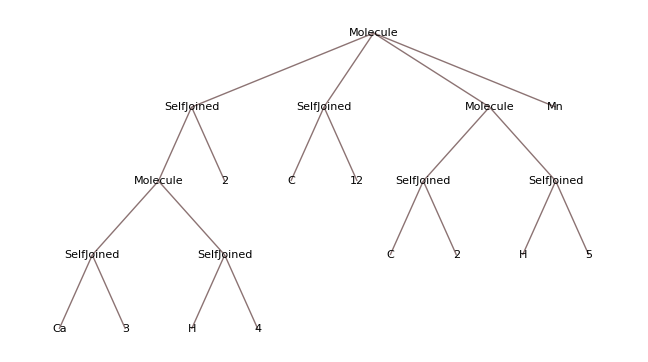

```mathematica
ParseMolecule["(Ca3H4)2C12(C2H5)Mn"]⟦1⟧
TreeForm[%]
```

```mathematica
MoleculeToAtoms[%%]
```

{{C,14},{Ca,6},{H,13},{Mn,1}}

{Molecule[SelfJoined[Molecule[SelfJoined[Ca,3],SelfJoined[H,4],SelfJoined[Molecule[SelfJoined[Ca,4],SelfJoined[O,3]],4]],2]],}

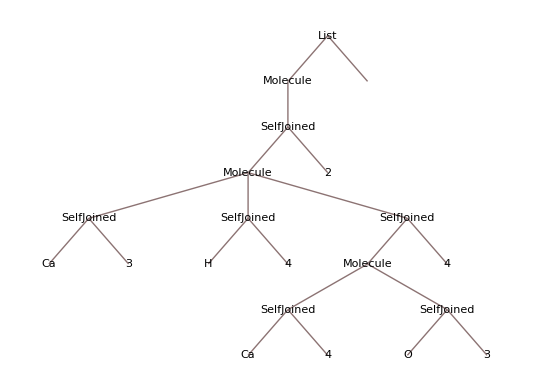

```mathematica
ParseMolecule["(Ca3H4(Ca4O3)4)2"]
TreeForm[%]
```

SelfJoined[Molecule[Molecule[SelfJoined[Ca,3],SelfJoined[H,4]],SelfJoined[Molecule[SelfJoined[Ca,4],SelfJoined[O,3]],4]],2]

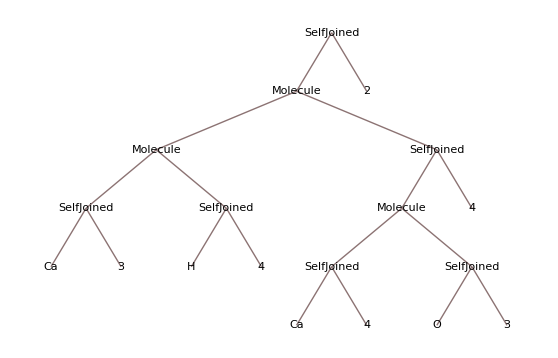

```mathematica
ParseMolecule["(Ca3H4(Ca4O3)4)2"]⟦1⟧
TreeForm[%]
```

## Miscellaneous

One of the most human activities is to create a basis of infinite objects. BNF is a way to build basis for a particular language.

The works of Noam Chomsky a very influential to the theory of compilers (and syntactic and semantic analysis).

Using grammar structures to produce jokes [Pau80]

This is the Interpreter design pattern presented in Gamma et al. [Gam94].

NIntegrate's Method option was implemented the technique described here.

## Exercises

1. Write BNF rules for specifying a postal address.

2. Choose a function from Mathematica like NIntegrate or NDSolve and write BNF for its signature and options.

3. Write a program that generates random molecules.

4. Using Exercise 3, generate, say, 200 molecules and find the minimal, maximal, mean, and median number of terminal symbols in them.

5. Using random molecules from Exercise 3 measure how long it takes for each implementation of MoleculeToAtoms to find the number of atoms of each element. Do timing measurements using one large molecule, and a certain number of small molecules.

6. Parse all the molecules from a class in ChemicalData, and categorize them according to their syntactical structure.

7. Define the functions CapitalLetterFirstQ, DigitFirstQ, LeftParethesisFirstQ, RightParethesisFirstQ, UnderscoreFirstQ in the section "Parser of chemical formulas" using regular expressions.

8. Using GraphPlot create the plot shown on Figure 2.1.

## Solutions

### Exercise 3: Program that generates random molecules

The solution we present is to program a random selection of the symbol sequences for each rule in the BNF form. In this solution we do not restrict the recursion depth, instead we rely on Mathematica's limiting of recursion process. (In other words, when $RecursionLimit is exceeded we will get messages.)

#### Definitions

```mathematica
Clear[RandomMolecule,RandomElement,RandomReplicated,RandomJoined]
elementNames=ElementData[#,"Abbreviation"]&/@ElementData[];
RandomMolecule[]:=
Block[{},
First[RandomSample[{RandomElement,RandomReplicated,RandomJoined},1]][]
];
RandomElement[]:=First[RandomSample[elementNames,1]];
RandomReplicated[]:=
Molecule[Replicated[RandomMolecule[],RandomInteger[{2,20}]]];
RandomJoined[]:=
Block[{},
Molecule[RandomMolecule[],RandomMolecule[]]
];
```

#### Experiments

Generate a random molecule:

```mathematica
rm=RandomMolecule[]
```

Molecule[Molecule[Replicated[Molecule[Molecule[Molecule[Re,Molecule[Replicated[Molecule[Molecule[Nb,Hs],Molecule[Sr,Molecule[Molecule[Replicated[Molecule[Molecule[Molecule[Ca,Uuq],Mn],Molecule[Replicated[Molecule[Replicated[Sn,10]],2]]],11]],Fe]]],18]]],Molecule[Replicated[Ra,18]]],Molecule[Replicated[V,18]]],5]],In]

Convert the molecule structure to a string:

```mathematica
MoleculeToString[rm]
```

At((Cu(P9)9)12)15

Find the depth of the expression tree and the number of terminal symbols:

```mathematica
{Depth[rm],NumberOfTerminals[rm]}
```

{11,7}

Show the tree of the expression representing the molecule

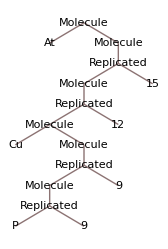

```mathematica
TreeForm[rm]
```

### Exercise 4: Statistics over random molecules

To find the number of terminal symbols we find all the strings and integers in a structure (using Cases).

#### Definitions

```mathematica
Clear[NumberOfTerminals]
NumberOfTerminals[m_String]:=1;
NumberOfTerminals[m_Molecule]:=
Length[Cases[m,_String,∞]]+Length[Cases[m,_Integer,∞]];
```

#### Experiments

Generate 200 random molecules:

```mathematica
rms=Table[RandomMolecule[],{200}];
```

Find descriptive statics on the depth and number of terminal symbols:

```mathematica
Through[{Min,Max,N[Mean[#]]&,Median,N[StandardDeviation[#]]&}[Depth/@rms]]
Through[{Min,Max,N[Mean[#]]&,Median,N[StandardDeviation[#]]&}[NumberOfTerminals/@rms]]
```

{1,185,13.355,7/2,29.943}

{1,1669,53.43,3,227.476}

Visualize the depth distribution:

```mathematica
Histogram[Sort[Depth/@rms],{1,184,1},PlotRange->All]
```

-Graphics-

```mathematica
Through[{Min,Max,N[Mean[#]]&,Median,N[StandardDeviation[#]]&}[NumberOfTerminals/@rms]]
```

{1,1669,53.43,3,227.476}

### Exercise 5: Profiling

```mathematica
rm={};
While[!(290≤ LeafCount[rm]≤300),rm=RandomMolecule[]]
```

```mathematica
MoleculeToAtoms/@Table[rm,{100}]; // Timing
```

{0.96343,Null}

### Exercise 6: Grouping by syntactic analysis trees

```mathematica
cfs=ChemicalData[#,"CompoundFormulaString"]&/@Apply[Join,ChemicalData[#]&/@ChemicalData["Classes"]];
cfs//Length
```

115486

```mathematica
pms=DeleteCases[First[ParseMolecule[#]]&/@cfs,First[$Failed]];
pms//Length
```

113297

```mathematica
mpatterns=Union[pms/.{s_String->(String),n_Integer->(Integer)}];
mpatterns//Length
```

113

```mathematica
pcounts=Count[pms,#]&/@(mpatterns/.{String->_String,Integer->_Integer})
```

{486,186,38,473,442,1153,5584,73,277,371,273,156,275,9210,18696,28,58,66,48,104,132,182,177,23,79,334,276,10601,14224,8683,10693,9,9,6,22,3,19,9,59,14,27,25,21,6,6,22,59,31,62,49,54,4178,4393,4347,2729,1889,1366,2560,1448,11,14,11,2,8,10,7,8,3,4,5,401,400,645,232,371,162,481,196,116,76,355,88,199,38,219,212,8,82,22,12,67,1,4,48,6,41,6,24,4,13,17,2,6,5,3,1,8,6,14,9,7,6,3}

{15,29,31,28}

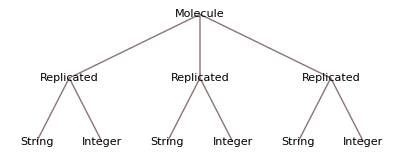
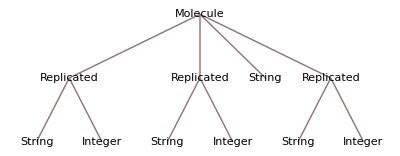
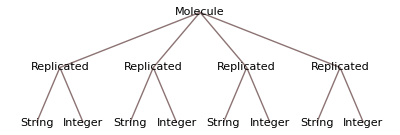
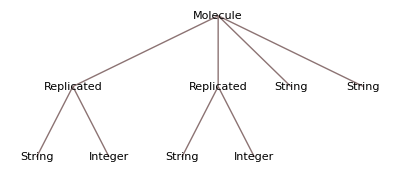
Number of formulas | Pattern
18696 | -Graphics-
14224 | -Graphics-
10693 | -Graphics-
10601 | -Graphics-

```mathematica
pos=Reverse@Ordering[pcounts,-4]
Grid[Prepend[Transpose[{pcounts⟦pos⟧,TreeForm[#,ImageSize->400]&/@mpatterns⟦pos⟧}],Style[#,Bold,Italic]&/@{"Number of formulas","Pattern"}],Dividers->{All,Join[{True,True},Table[False,{Length[pos]-1}],{True}]}]
```

```mathematica
BarChart[Sort@pcounts,PlotRange->All]
```

-Graphics-

```mathematica
BarChart[Sort@Log@pcounts,PlotRange->All]
```

-Graphics-

### Exercise 7: Regular expressions matchings

```mathematica
DigitFirstQ[s_String]:=StringMatchQ[s,RegularExpression["^\\d.*"]];
```

```mathematica
CapitalLetterFirstQ[s_String]:=StringMatchQ[s,RegularExpression["^[A-Z].*"]];
```

```mathematica
LeftParethesisFirstQ[s_String]:=StringMatchQ[s,RegularExpression["^\\(.*"]];
```

```mathematica
RightParethesisFirstQ[s_String]:=StringMatchQ[s,RegularExpression["^\\).*"]];
```

```mathematica
UnderscoreFirstQ[s_String]:=StringMatchQ[s,RegularExpression["^\\_.*"]];
```

## References

[Kle01] Klein, U. (2001). Tools and modes of representation in the laboratory sciences. pp. 47- "Conventionalities in formula writing". Kluwer, http://www.pierrelaszlo.com/articles/history-of-chemistry/54-conventionalities-in-formula-writing

[Gam94] Gamma, E., Helm, R., Johnson, R., and Vlissides, J (1994). Design Patterns: Elements of Reusable Object-Oriented Software. Addison-Wesley.

[Wat89] Watson, D. (1989). High Level Languages and Their Compilers. Addison-Wesley.

[Pau80] Paulos, J. A. (1980). Mathematics and Humor, The University of Chicago Press.

## Section hyperlinks

```mathematica
Hyperlink[Style["Everything is an expression","Text",FontSize->12],"paclet:tutorial/EverythingIsAnExpression"]
```

```mathematica
Hyperlink[Style["Expressions","Text",FontSize->12],"paclet:guide/Expressions"]
```

```mathematica
Hyperlink[Style["Tally","Program"],"paclet:ref/Tally"]
```

## Misc code

### The basic idea

<molecule>
<connected>  /  by the rule <molecule>
<molecule><molecule>  /  by the rule <connected>
<connected><connected> / by the rule <molecule>
<molecule><molecule><molecule><molecule>  / by the rule <connected>
<element><element><element><replicated>   / by the rule <molecule>
<element><element><element><element><number> / by the rule <replicated>